# Padé approximation

## Algorithm

```mathematica
Clear[pade]
pade[f_,n_Integer]:=Module[
{
a,b,
c,
res,hankelMatrix
},
c=CoefficientList[Series[f,{x,0,2n+2}],x];
hankelMatrix=Table[c⟦i+j⟧,{j,4,n+3},{i,0,n-1}];
res=Table[c⟦i⟧,{i,n+4,2n+3}];
b=Composition[Abs,Prepend[#,1]&,Reverse][LinearSolve[hankelMatrix,res]];
a=Dot[Take[b,{1,#}],Reverse[Take[c,{1,#}]]]&/@Range[n+1];
Sum[a⟦i+1⟧x^i,{i,0,n}]/Sum[b⟦i+1⟧x^i,{i,0,n}]
]
```

## Examlple №1

```mathematica
f1=1/(1+Sin[x^2])
n1=6;
res1=pade[f1,n1]
```

1/(1+Sin[x^2])

(1+(11 x^2)/686+(3 x^4)/49+(8647 x^6)/41160)/(1+(697 x^2)/686+(53 x^4)/686+(4307 x^6)/41160)

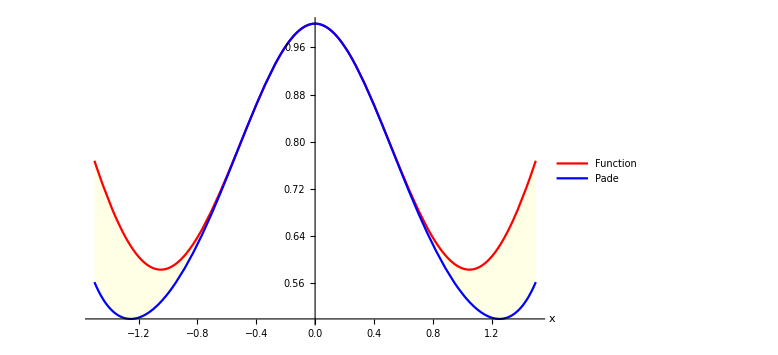

```mathematica
Plot[{res1,f1},{x,-1.5,1.5},
PlotLegends->{"Function", "Pade"},
AxesLabel->Automatic,
Filling->{1->{2}},
FillingStyle->Directive[Opacity[0.1],Yellow],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №2

```mathematica
f2=√((1+1/2 x)/(1+2x))
n2=2;
res2=pade[f2,n2]
```

√((1+x/2)/(1+2 x))

(1+(76577 x)/32486+(307441 x^2)/259888)/(1+(201883 x)/64972+(1192703 x^2)/519776)

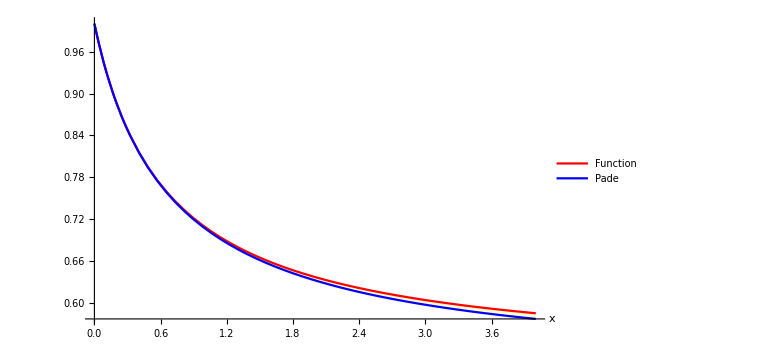

```mathematica
Plot[{res2,f2},{x,0,4},
PlotLegends->{"Function", "Pade"},
AxesLabel->Automatic,
Filling->{1->{2}},
FillingStyle->Directive[Yellow],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №3

```mathematica
f3=Log[1+x]
n3=2;
res3=pade[f3,n3]
```

Log[1+x]

(x+(5 x^2)/6)/(1+(4 x)/3+(2 x^2)/5)

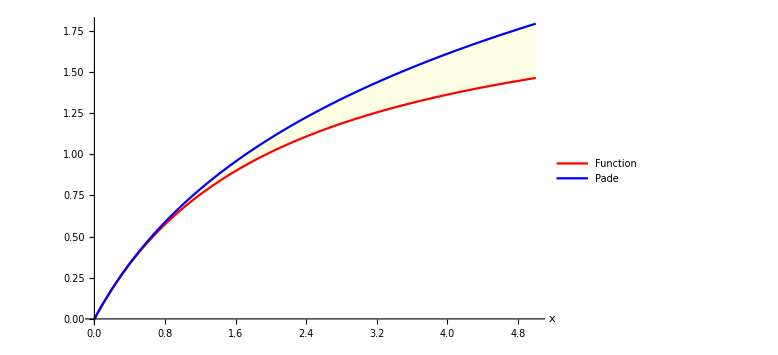

```mathematica
Plot[{res3,f3},{x,0,5},
PlotLegends->{"Function", "Pade"},
AxesLabel->Automatic,
Filling->{1->{2}},
FillingStyle->Directive[Opacity[0.1],Yellow],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №4

```mathematica
f4=ⅇ^-x/(1+x)
n4=4;
res4=pade[f4,n4]
```

ⅇ^-x/(1+x)

(1-(385398 x)/580625+(47907 x^2)/232250-(40762 x^3)/1045125+(62767 x^4)/13006000)/(1+(775852 x)/580625+(219909 x^2)/580625+(232882 x^3)/5225625+(1203329 x^4)/585270000)

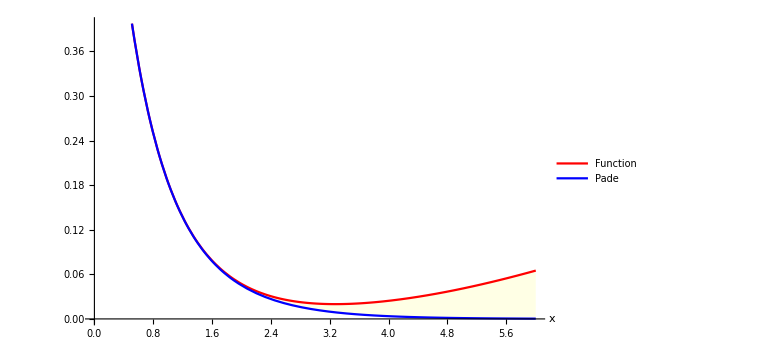

```mathematica
Plot[{res4,f4},{x,0,6},
PlotLegends->{"Function", "Pade"},
AxesLabel->Automatic,
Filling->{1->{2}},
FillingStyle->Directive[Opacity[0.1],Yellow],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```

## Example №5

```mathematica
f5=Log[1+x]/(√(1+x))
n5=3;
res5=pade[f5,n5]
```

Log[1+x]/(√(1+x))

(x+(32902 x^2)/33451+(315943 x^3)/2809884)/(1+(66353 x)/33451+(2131193 x^2)/1873256+(142053 x^3)/936628)

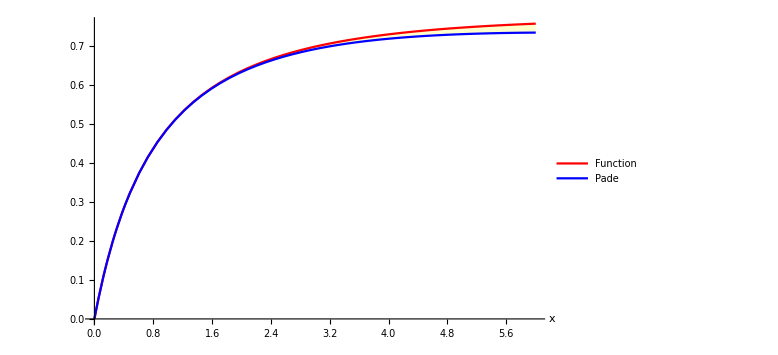

```mathematica
Plot[{res5,f5},{x,0,6},
PlotLegends->{"Function", "Pade"},
AxesLabel->Automatic,
Filling->{1->{2}},
FillingStyle->Directive[Yellow],
PlotStyle->{{Red},{Blue}},
ImageSize->Large]
```